# Fertility And Development

Written by Mark Lauer, August 30th, 2009
Last updated September 6th, 2009
This program is hereby released to the public domain for any purpose.

This notebook generates graphics from the data used in the paper:
Mikko Myrskylä, Hans-Peter Kohler & Francesco C. Billari (2009)
"Advances in development reverse fertility declines"
Nature 460, 741-743 (6 August 2009) | doi:10.1038/nature08230
http://www.nature.com/nature/journal/v460/n7256/full/nature08230.html

## Import Data

Download and import the data

```mathematica
dataurl = "http://www.nature.com/nature/journal/v460/n7256/extref/nature08230-s2.zip";data = First[Import[dataurl, "*"]];
TableForm[data[[Range[5], Range[10]]]]
```

country | HDI.1975 | HDI.1976 | HDI.1977 | HDI.1978 | HDI.1979 | HDI.1980 | HDI.1981 | HDI.1982 | HDI.1983
Albania |  |  |  |  |  | 0.731273 | 0.734932 | 0.737146 | 0.738452
Algeria | 0.565067 | 0.570966 | 0.575103 | 0.581995 | 0.587976 | 0.590365 | 0.593946 | 0.599331 | 0.605605
Angola | 0.427032 | 0.427252 | 0.427463 | 0.428155 | 0.428839 | 0.429516 | 0.424447 | 0.422965 | 0.423151
Argentina | 0.796896 | 0.796294 | 0.800532 | 0.798749 | 0.804949 | 0.807989 | 0.805496 | 0.80343 | 0.805606

Extract and remove the list of countries and column headings, then report the length of each

```mathematica
countrylist = Rest[data[[All,1]]];
headinglist = Rest[data[[1]]];
data = Drop[data, 1, 1];TableForm[{{"Countries: ",Length[countrylist]},{"Columns: ", Length[headinglist]}}]
```

Countries:  | 143
Columns:  | 124

A function to parse column headings and define corresponding Mathematica functions from the values.
For example, "HDI.1975" leads to defining HDI[countryname, 1975]

```mathematica
Store[value_, {country_Integer, columnname_Integer}] :=
Module[{type, year},
{type, year} = StringSplit[headinglist[[columnname]], "."];
(Symbol[type][countrylist[[country]], ToExpression[year]]) = If[NumberQ[value], value, Missing[]]
]
```

Apply this across all the data

```mathematica
MapIndexed[Store, data, {2}];
```

Check this with a couple of plots

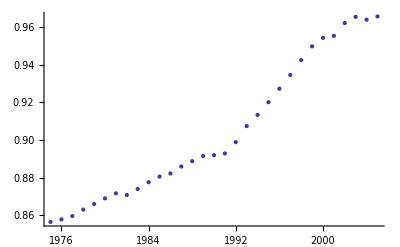

```mathematica
ListPlot[Table[{y, HDI["Australia", y]}, {y, 1975, 2005}]]
```

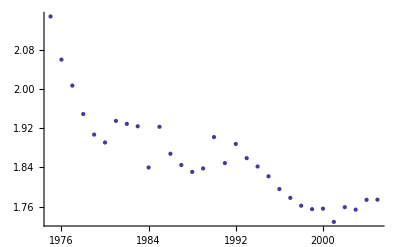

```mathematica
ListPlot[Table[{y, TFR["Australia", y]}, {y, 1975, 2005}]]
```

Generate a scatter plot of all countries' TFR against HDI in 1975 and 2005

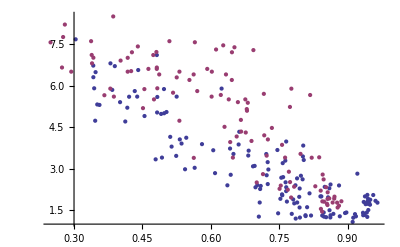

```mathematica
ListPlot[{
{HDI[#, 2005], TFR[#, 2005]}& /@ countrylist, 
{HDI[#, 1975], TFR[#, 1975]}& /@ countrylist} 
]
```

Generate a similar plot, but with distorted axes, as the paper does, to make differences at low fertility and high development look much more significant

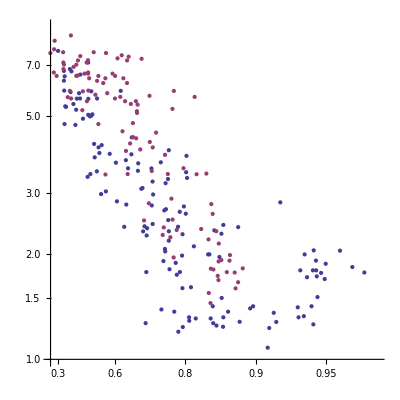

```mathematica
ListLogPlot[{
{-Log[1-HDI[#, 2005]], TFR[#, 2005]}& /@ countrylist, 
{-Log[1-HDI[#, 1975]], TFR[#, 1975]}& /@ countrylist} , Ticks -> {{-Log[1-#], #}& /@ {0.3, 0.6, 0.8, 0.9, 0.95}, Automatic},
PlotRange -> {{-Log[1-0.25], 3.5}, {1, 9}},
AspectRatio -> 1
]
```

## Match Countries To Mathematica Country Data

Define an equivalent list of countries using Mathematica names by expanding some abbreviations and removing spaces

```mathematica
canonicallist = (countrylist /.{"USA" -> "UnitedStates", "Congo, Dem. Rep." -> "DemocraticRepublicCongo","Congo, Rep." -> "RepublicCongo", "Cote d'Ivoire" -> "IvoryCoast", "Kyrgyz Republic" -> "Kyrgyzstan", "NL" -> "Netherlands", "S. Korea" -> "SouthKorea", "Slovak Republic" -> "Slovakia", "Trinidad and Tobago" -> "TrinidadTobago",
"Lao" -> "Laos", x_String :> StringReplace[x, {" " -> ""}]});
```

Check that every country in the data matches one in Mathematica

```mathematica
Complement[canonicallist, CountryData["Countries"]]=={}
```

True

## Key Functions

Define (self-cacheing) function to map countries to the Mathematica names using the list

```mathematica
CanonicalName[country_String] :=
(CanonicalName[country] = canonicallist[[First[First[Position[countrylist, country]]]]])
```

Check this for three countries

```mathematica
CanonicalName /@ {"USA", "New Zealand", "United Kingdom"}
```

{UnitedStates,NewZealand,UnitedKingdom}

Get list of continents for countries

```mathematica
continentslist = Union[CountryData[CanonicalName[#], "Continent"]& /@ countrylist]
```

{Africa,Asia,Europe,NorthAmerica,Oceania,SouthAmerica}

Define (self-cacheing) function to map countries to continents

```mathematica
ContinentOf[country_String] :=
(ContinentOf[country] = CountryData[CanonicalName[country], "Continent"])
```

Check this for four countries

```mathematica
ContinentOf /@ {"USA", "China", "Israel", "Australia"}
```

{NorthAmerica,Asia,Asia,Oceania}

Define ColourOf[] function from continents to colours by splitting the (reversed) DarkRainbow spectrum,
then display all values

```mathematica
MapThread[Set, {ColourOf /@ Reverse[continentslist], ColorData["DarkRainbow"]/@ (Range[Length[continentslist]]/Length[continentslist])}];
Style[#, FontColor -> ColourOf[#]]& /@ continentslist
```

{Africa,Asia,Europe,NorthAmerica,Oceania,SouthAmerica}

Define (self-cacheing) function to map countries to their populations according to Mathematica

```mathematica
PopulationOf[country_String] :=
(PopulationOf[country] = CountryData[CanonicalName[country], "Population"])
```

Check this for four countries

```mathematica
PopulationOf /@ {"USA", "China", "Israel", "Australia"}
```

{3.02841×10^8,1.29801×10^9,6.80999×10^6,2.05304×10^7}

## Animated Charts

Define function to plot a bubble chart of Total Fertility Rate against Human Development Index for a given year.  Bubble sizes are determined by population, colours by continent.

```mathematica
SnapshotChart[year_Integer, chartoptions___] :=
BubbleChart[{
(* Ensure legend appears in fixed order by "plotting" continents *)
Legended[Style[{0,0, 1}, ColourOf[#]], Style[#, Small]]& 
/@ continentslist,
(* Add bubble for each country *) 
Style[
(* On mouse-over, display country names *)
Tooltip[
{HDI[#, year], TFR[#, year], PopulationOf[#]},
#],
ColourOf[ContinentOf[#]]
]& /@ countrylist},
chartoptions,
BubbleSizes -> {0.01, 0.15}, PlotRange -> {{0.2, 1.0}, {0.8, 9}},
FrameLabel -> {"Human Development Index", "Total Fertility Rate"}, PlotLabel -> ToString[year]
]
```

Check this for one year

```mathematica
SnapshotChart[2002]
```

-Graphics--Graphics- | Africa
-Graphics- | Asia
-Graphics- | Europe
-Graphics- | NorthAmerica
-Graphics- | Oceania
-Graphics- | SouthAmerica

Use Mathematica's built in dynamic graphics to view animation through time

```mathematica
Animate[SnapshotChart[y],{y, 1975, 2005, 1}, AnimationRunning -> False, DisplayAllSteps -> True]
```

Generate an animated GIF of all thirty years 
(Note: mouse-over will no longer work outside Mathematica)

```mathematica
Export["FertilityAndDevelopment.gif", Table[SnapshotChart[y], {y, 1975, 2005, 1}], ImageSize -> 440]
```

FertilityAndDevelopment.gif

Generate an animated GIF of all thirty years, zooming in to region with advanced countries 
(Note: mouse-over will no longer work outside Mathematica)

```mathematica
Export["FertilityAndDevelopmentDetail.gif", Table[
SnapshotChart[y, PlotRange -> {{0.7, 1.0}, {0.8, 4}}],
 {y, 1975, 2005, 1}], ImageSize -> 440]
```

FertilityAndDevelopmentDetail.gif

## Trajectory Plots

Use the threshold found by the paper as the HDI level at which TFR changes direction

```mathematica
bouncethreshold = 0.86;
```

Find countries which reach or exceed this threshold at some point in available data

```mathematica
advanced = Select[countrylist, (Max[Table[HDI[#, i], {i, 1975, 2005}]]≥ bouncethreshold)&]
```

{Argentina,Australia,Austria,Belgium,Canada,Cyprus,Denmark,Finland,France,Germany,Greece,Hungary,Iceland,Ireland,Israel,Italy,Japan,S. Korea,Kuwait,Luxembourg,Malta,NL,New Zealand,Norway,Portugal,Spain,Sweden,Switzerland,United Arab Emirates,United Kingdom,USA}

Define a function to determine the first year in which a country's HDI exceeds a given threshold

```mathematica
ReferenceYear[country_String, developmentthreshold_Real] :=
Min[
Select[Range[1975, 2005], 
(HDI[country, #]≥ developmentthreshold)&]
]
```

Check this function using the paper's threshold for all advanced countries

```mathematica
TableForm[SortBy[
{#, ReferenceYear[#, bouncethreshold]}& /@ advanced,
Last]]
```

Canada | 1975
Denmark | 1975
NL | 1975
Norway | 1975
Sweden | 1975
Switzerland | 1975
USA | 1975
France | 1976
Japan | 1976
Australia | 1978
Belgium | 1978
Finland | 1978
Iceland | 1978
Austria | 1980
Italy | 1981
New Zealand | 1982
Spain | 1982
United Kingdom | 1982
Germany | 1983
Luxembourg | 1984
Israel | 1985
Ireland | 1990
Greece | 1992
Cyprus | 1995
Portugal | 1997
S. Korea | 1997
Malta | 2001
Kuwait | 2003
United Arab Emirates | 2004
Argentina | 2005
Hungary | 2005

Define a function to return the time series of TFR for a given country beginning in its reference year (measured as absolute difference from the TFR in the reference year).

```mathematica
TFRSeriesFromReference[country_String, threshold_Real]:=
If[ReferenceYear[country, threshold]>2005, 
(* Return empty series when HDI never reached threshold *)
{},
Table[TFR[country, y], {y, ReferenceYear[country, threshold], 2005}]-TFR[country, ReferenceYear[country, threshold]]
]
```

Check this function for Australia

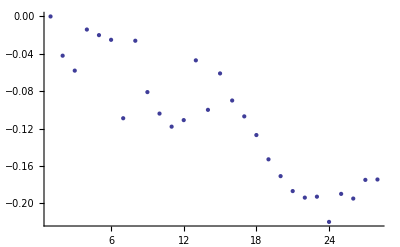

```mathematica
ListPlot[TFRSeriesFromReference["Australia", bouncethreshold]]
```

Define a reasonable colour scheme

```mathematica
stylescheme = Reverse[ColorData["DarkRainbow"]/@ (Range[Length[advanced]]/Length[advanced])];
```

Build a chart of these time series for all advanced countries

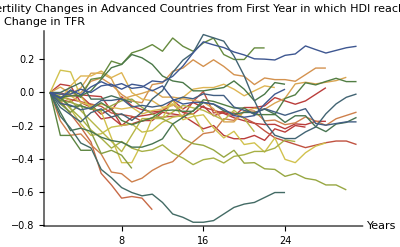

```mathematica
g0 = ListPlot[
Cases[ 
TFRSeriesFromReference[#, bouncethreshold]& /@ advanced, 
(* Eliminate empty series *)
 {_,___}], 
Joined -> True,
PlotStyle -> stylescheme,PlotLabel -> "Total Fertility Changes in Advanced Countries\nfrom First Year in which HDI reaches "<>ToString[bouncethreshold],AxesLabel -> {"Years", "Change in TFR"}]
```

Generate a PNG file containing this chart

```mathematica
Export["FertilitySeries.png", g0, ImageSize -> 420]
```

FertilitySeries.png

Define a function to return a pair of changes, the first being the absolute change in HDI,
the second being the absolute change in TFR, between the reference year and 2005.

```mathematica
ChangeFromReference[country_String, threshold_Real]:=
Module[{refyear = ReferenceYear[country, threshold]},
If[refyear>2005, {Infinity, Infinity},
{HDI[country, 2005]-HDI[country, refyear],
TFR[country, 2005]-TFR[country, refyear]}
]
]
```

Plot these changes in a scatter plot for all advanced countries

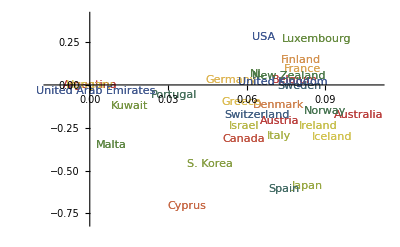

```mathematica
g1 = ListPlot[{ChangeFromReference[#, bouncethreshold]}& /@ advanced, PlotMarkers -> advanced, PlotRange -> {{-0.015, 0.11}, {-0.8, 0.4}},PlotStyle -> stylescheme]
```

The paper fits a model in which countries with HDI above the 0.86 threshold see increasing TFR with increasing HDI, according to which "on average an HDI increase of 0.05 results in an increase of the TFR by 0.204".
Build a plot illustrating this rate of increase for later addition to the plot above.

```mathematica
g2 = ListPlot[{{0,0},{0.1, 0.408}}, Joined -> True, PlotRange -> All, PlotStyle ->  {{Red, Thick, Dashed}}];
```

Define a function to return a complete trajectory of changes in HDI and TFR between the reference year and 2005 (both measured relative to their value in the reference year).

```mathematica
TrajectoryFromReference[country_String, threshold_Real]:=
Module[{refyear = ReferenceYear[country, threshold]},
If[refyear>2005, 
(* Keep non-advanced countries off plots *) 
{{Infinity, Infinity}},
Table[
{HDI[country, y]-HDI[country, refyear],
TFR[country, y]-TFR[country, refyear]}, 
{y, refyear, 2005}]
]
]
```

Build a plot which includes all these trajectories for advanced countries, then display these together with the scatter plot and fitted model plot above

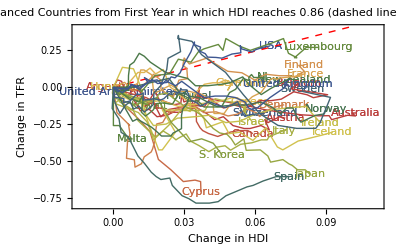

```mathematica
(* Build trajectory plot *)
g3 = ListPlot[
TrajectoryFromReference[#, bouncethreshold]& /@ advanced,  
PlotStyle -> stylescheme,
Joined -> True];
(* Display all three graphs together with nice axes *)
g4 = Show[g1,g2, g3, PlotRange -> {{-0.015, 0.112}, {-0.8, 0.4}},FrameLabel -> {"Change in HDI", "Change in TFR"}, Axes -> True, AxesStyle -> GrayLevel[0.7], Frame -> {{True, False}, {True, False}},PlotLabel -> "Trajectories of Advanced Countries\nfrom First Year in which HDI reaches "<>ToString[bouncethreshold]<>"\n(dashed line is model fitted by the paper)"]
```

Generate a PNG file containing this chart

```mathematica
Export["FertilityTrajectories.png", g4, ImageSize -> 420]
```

FertilityTrajectories.png

## Simulating Bias

Because the reference year is chosen to be the year (within a window) that is lowest, there is a statistical bias for subsequent trajectories to rise.  To investigate this, let's run some simulations.

First though, how long do countries spend in the window?

```mathematica
Select[(ReferenceYear[#, 0.9]-ReferenceYear[#, 0.85])& /@ advanced , 
NumberQ]//Mean//N
```

15.1667

Since the entire data set is 30 years, countries spend on average more than half the available time inside the window.  This is plenty of time to create a significant bias by choosing the lowest TFR within the window as the threshold year.

Let's build a simulation to measure how large the bias might be.  For this purpose, we will need to know the mean ("drift") and standard deviation ("vol") of yearly changes in the TFR and HDI.  We will compute these from all advanced countries, for all years in which those countries have an HDI of at least 0.85.  

Define globals TFRDrift and TFRVol by estimation from the data

```mathematica
Block[{changes},
changes = Join@@(Differences[TFRSeriesFromReference[#, 0.85]]&/@ advanced);

TableForm[
{Length[changes],
TFRDrift = Mean[changes], 
TFRVol = StandardDeviation[changes]},
TableHeadings -> {{"Count", "Drift", "Vol"}}
]
]
```

Count | 695
Drift | -0.0104077
Vol | 0.051503

Notice that the overall mean change in TFR is negative (even though the paper's conclusion implies it should be positive)

Define a function to return the time series of HDI for a given country beginning in its reference year

```mathematica
HDISeriesFromReference[country_String, threshold_Real]:=
If[ReferenceYear[country, threshold]>2005, 
(* Return empty series when HDI never reached threshold *)
{},
Table[HDI[country, y], {y, ReferenceYear[country, threshold], 2005}]
]
```

Define globals HDIDrift and HDIVol by estimation from the data

```mathematica
Block[{changes},
changes = Join@@(Differences[HDISeriesFromReference[#, 0.85]]&/@ advanced);

TableForm[
{Length[changes],
HDIDrift = Mean[changes], 
HDIVol = StandardDeviation[changes]},
TableHeadings -> {{"Count", "Drift", "Vol"}}
]
]
```

Count | 695
Drift | 0.00298587
Vol | 0.00242817

In the simulation, we will generate paths using random walks with the above parameter estimates, in each case beginning where the country was in its reference year.  Let's check when and where the advanced countries were in their reference year

```mathematica
TableForm[SortBy[
{ReferenceYear[#, 0.85], 
TFR[#, ReferenceYear[#, 0.85]],
HDI[#, ReferenceYear[#, 0.85]]}& /@ advanced,
Last], TableHeadings -> {advanced, {"Reference\nYear", "TFR", "HDI"}}]
```

| Reference
Year | TFR | HDI
Argentina | 1979 | 1.48 | 0.850029
Australia | 1988 | 2.17 | 0.85014
Austria | 1999 | 2.5962 | 0.850206
Belgium | 1976 | 1.74 | 0.850449
Canada | 1978 | 1.38 | 0.851897
Cyprus | 1977 | 2.649 | 0.851992
Denmark | 1980 | 3.242 | 0.851993
Finland | 1988 | 1.5 | 0.852366
France | 1995 | 1.65 | 0.852627
Germany | 1975 | 2.331 | 0.852847
Greece | 2000 | 2.462 | 0.852974
Hungary | 1978 | 1.87 | 0.853243
Iceland | 1994 | 2.23 | 0.853904
Ireland | 1996 | 1.43 | 0.854027
Israel | 1977 | 1.641 | 0.854348
Italy | 2003 | 1.27 | 0.854506
Japan | 2001 | 2.6402 | 0.854852
S. Korea | 1975 | 1.736 | 0.8549
Kuwait | 1976 | 2.529 | 0.855281
Luxembourg | 1975 | 1.688 | 0.855986
Malta | 1975 | 1.909 | 0.856136
NL | 1975 | 2.148 | 0.856418
New Zealand | 2000 | 1.72 | 0.858329
Norway | 1975 | 1.927 | 0.859947
Portugal | 1975 | 1.779 | 0.867326
Spain | 1975 | 1.919 | 0.870765
Sweden | 1975 | 1.991 | 0.871365
Switzerland | 1975 | 1.774 | 0.877182
United Arab Emirates | 1975 | 1.598 | 0.878232
United Kingdom | 1975 | 1.664 | 0.881259
USA | 1975 | 1.824 | 0.88653

So most countries are starting near the bottom of the window, and all are within it.

Define a function that takes the development and fertility paths of a country, and implements the threshold finding rule given in the paper with respect to a given window, namely find the lowest value of TFR while the country's HDI is within the window.  Return the position within the path where this lowest value of TFR  is first attained within the window.

```mathematica
FindThreshold[development_List, fertility_List, windowstart_Real, windowend_Real]:=
Module[{eligible, lowestvalue, candidates},

(* Find positions where development is within window *)
eligible= Position[development, d_Real /; (d ≥ windowstart&& d ≤ windowend), {1}];

(* Return last position if there are no eligible ones *)
If[eligible == {}, Return[Length[fertility]]];

(* Determine lowest fertility amongst eligible positions *) 
lowestvalue = Min[Extract[fertility, eligible]];

(* Find positions of this lowest fertility *)
candidates = Position[fertility, lowestvalue, {1}];

(* Return first such position that is eligible *)
First[First[Intersection[candidates, eligible] ]]
]
```

Let's unit test this function by applying it to random series.

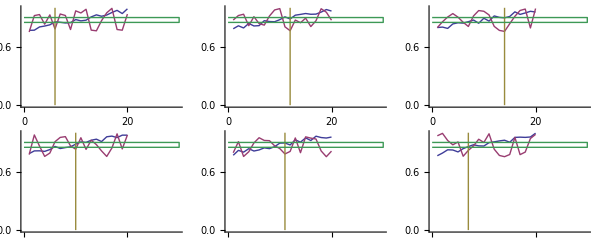

```mathematica
GraphicsGrid[Partition[Table[
Block[{d, f, s},
(* make random development series trending upwards from 0.75 to 1.0 *) 
d = 0.75+RandomReal[0.05, 20]+Range[20]/100;
(* make random fertility series between 0.75 to 1.0 *) 
f = 0.75+RandomReal[0.25, 20];
(* apply function *)
s = FindThreshold[d, f, 0.85, 0.9];
(* display series, found position and window range *)
ListPlot[{d, f, {{s, 0}, {s, 1}}, {{0, 0.85}, {30, 0.85}, {30, 0.9}, {0, 0.9}}}, Joined-> True]
],
{6}],3]]
```

Define a function to generate paths according to a given step distribution.
Note that paths will have (steps+1) elements, the first always being zero;
in this way, the caller can add a constant to change the start value

```mathematica
GeneratePath[distribution_, steps_Integer]:=
Module[{changes},
changes = RandomReal[distribution, steps];
FoldList[Plus, 0, changes]
]
```

Check this function by plotting a few random walk paths with drift 
(use vol of 1 and length of 16, so final standard deviation is 4)

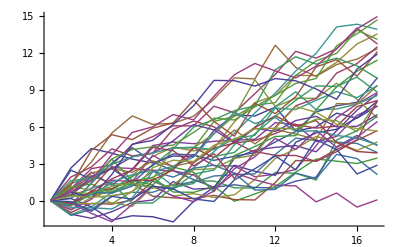

```mathematica
ListPlot[Table[GeneratePath[NormalDistribution[0.5, 1], 16], {40}], Joined -> True]
```

Define a function to generate a path for both development and fertility in the given country, beginning at the values in the country's reference year, but remove the part of the path prior to reaching the HDI threshold according to the paper's definition.  
Return the resulting path as a list of pairs, expressed relative to the starting point.
Let the HDI evolve with drift and vol equal to the overall values for advanced countries found above.   
Let the TFR evolve with vol equal to the overall value for advanced countries found above,
but with zero drift.
Warning: Uses global variables HDIDrift, HDIVol, TFRVol

```mathematica
GeneratePostThresholdPath[country_String, windowstart_Real, windowend_Real] :=
Module[{ y0, f, d, threshold},

(* Find reference year *)
y0 = ReferenceYear[country, windowstart];

(* Generate complete path from reference year *)
d = GeneratePath[NormalDistribution[HDIDrift, HDIVol], 2005-y0]
+HDI[country, y0];
f = GeneratePath[NormalDistribution[0, TFRVol], 2005-y0]
+TFR[country, y0];

(* Determine when country passes threshold according to paper *)
threshold = FindThreshold[d, f, windowstart, windowend];

(* Remove ealier part of path and return as pairs relative to this *)
d = Drop[d, threshold -1];
f = Drop[f, threshold -1];
Transpose[{d-First[d], f-First[f]}]
]
```

Check this function by plotting the resulting trajectories of Australia for a few trials

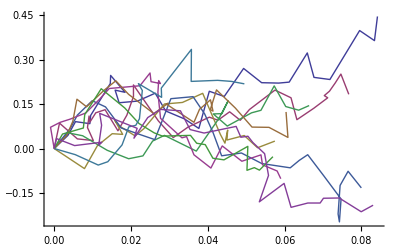

```mathematica
ListPlot[Table[GeneratePostThresholdPath["Australia", 0.85, 0.9], {10}], Joined -> True]
```

Simulate one path for each advanced country, and show these paths with fitted slope from paper

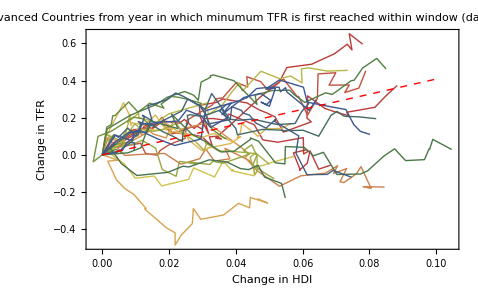

```mathematica
g5 = Show[
ListPlot[Map[GeneratePostThresholdPath[#, 0.85, 0.9]&, advanced], Joined -> True, PlotStyle -> stylescheme], 
g2, 
FrameLabel -> {"Change in HDI", "Change in TFR"}, Axes -> True, AxesStyle -> GrayLevel[0.7], Frame -> {{True, False}, {True, False}},PlotLabel -> "Random Trajectories of Advanced Countries from\nyear in which minumum TFR is first reached within window\n(dashed line is model fitted by the paper)"]
```

```mathematica
Export["FertilitySimulationExample.png", g5, ImageSize -> 420]
```

FertilitySimulationExample.png

So now the fitted slope from the paper looks more plausible, even though we actually generated the data using zero drift in TFR.  Notice that paths tend to have upward trajectories early on -- this is because HDI tends to be still within the window, in which case falls in fertility lead to the threshold being moved.

Now we can measure the size of the bias, at least under this simplified model, by running many such simulations and fitting a relationship between TFR and HDI each time.

Define a function to compute changes in the paths generated above

```mathematica
PathChanges[path_List] :=
If[Length[path]<2, 
{{0,0}},
Transpose[Map[Differences, Transpose[path]]]
]
```

Define a function to sample one path per country and use this to fit a proportional relationship between development and fertility.  Returns the slope of best fit.
Warning: Call to GeneratePostThresholdPath uses global variables HDIDrift, HDIVol, TFRVol

```mathematica
SampleMethod[windowstart_Real, windowend_Real]:=
Module[{allchanges, fit, x},

(* Gather together all the changes in all paths of one run per country *)
allchanges = Join@@Map[
PathChanges[GeneratePostThresholdPath[#, 0.85, 0.9]]&, 
advanced];

(* Use least squares to fit the slope of TFR against HDI *)
fit = Fit[allchanges, x, x];
(* Return slope *)
Coefficient[fit, x]
]
```

The above function effectively simulates the paper's methodology, under a simplified model, in a case where there is no connection between fertility and development at all.
Let's call it 100 times and plot the results.

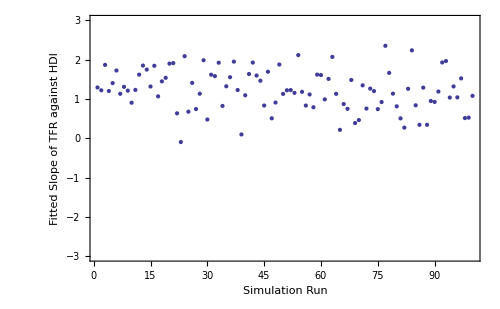

```mathematica
ListPlot[Table[SampleMethod[0.85, 0.9], {100}], 
PlotRange -> {All, {-3,3}},
Axes -> {True, False}, Frame -> {{True, False}, {True, False}},
FrameLabel -> {"Simulation Run", "Fitted Slope of TFR against HDI"}]
```

The bias in the methodology is clear, the resulting fit is almost always above zero, despite the true drift being zero.  Let's look at a historgram of the results, and check the mean and 90% quantile.

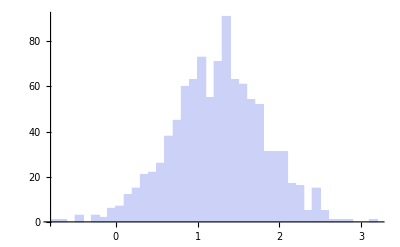

```mathematica
Histogram[sample = Table[SampleMethod[0.85, 0.9], {1000}], {0.1}]
```

```mathematica
{Mean[sample], Quantile[sample, 0.9]}
```

{1.24818,1.96534}

So the typical size of the bias is around 1.25, with values up to 2 being reasonably likely.  However, this is less than the value of 4.08 found in the paper.  So we have only explained half of their result.

For interest, let's check how likely we are to get a zero result from their methdology.

```mathematica
Count[sample, z_/; z≤ 0]/Length[sample]+0.0
```

0.016

So the paper's method only generates the true value or zero, or less, about 1-2% of the time,
and values above 2 about 10% of the time, under this simplified model.